# C-REX 2 GEMINI Inputs

```mathematica
x2=Subdivide[-1.6 10^6,1.6 10^6,32];
x3=Range[-100 10^3,100 10^3,1 10^3];
Bmag=50000 10^-9;
Qamp=0.75;
Qwth=10 10^3;
Qpos=10 10^3;
Eamp=300;
Emin=200;
Ewth=10 10^3;
Epos=10 10^3;
Famp=-500;
Fwth= 20 10^3;
Fpos=0;
```

## Precipitation

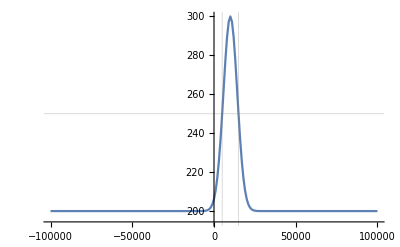

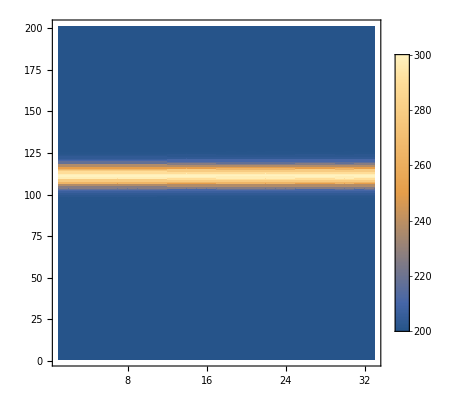

```mathematica
E0[x_,y_,A_,Ab_,d_,w_]:=(A-Ab) Exp[-(y-d)^2 4Log[2]/w^2]+Ab
E0plot=Table[E0[x,y,Eamp, Emin,Epos,Ewth],{x,x2},{y,x3}];
ListLinePlot[Transpose[{x3,E0plot[[1,;;]]}],PlotRange->All,GridLines->{Epos+Ewth{-1,1}/2,{Emin+(Eamp-Emin)/2}}]
ListDensityPlot[E0plot//Transpose,InterpolationOrder->0,PlotLegends->Automatic,PlotRange->All]
```

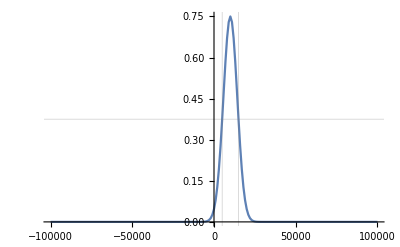

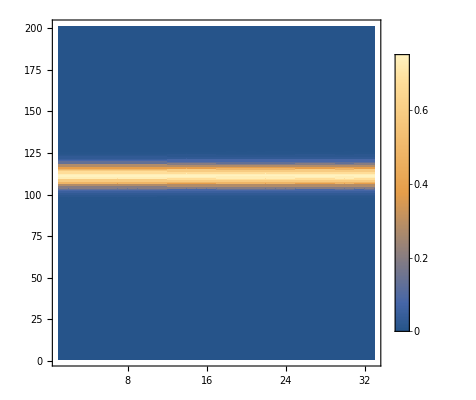

```mathematica
Q[x_,y_,A_,d_,w_]:=A Exp[-(y-d)^2 4Log[2]/w^2]
Qplot=Table[Q[x,y,Qamp,Qpos,Qwth],{x,x2},{y,x3}];
ListLinePlot[Transpose[{x3,Qplot[[1,;;]]}],PlotRange->All,GridLines->{Qpos+Qwth{-1,1}/2,{Qamp/2}}]
ListDensityPlot[Qplot//Transpose,InterpolationOrder->0,PlotLegends->Automatic,PlotRange->All]
```

## Flow Burst

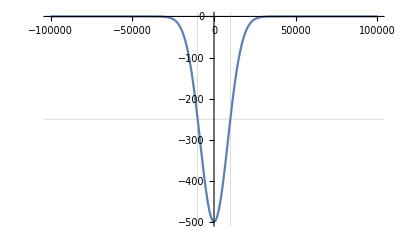

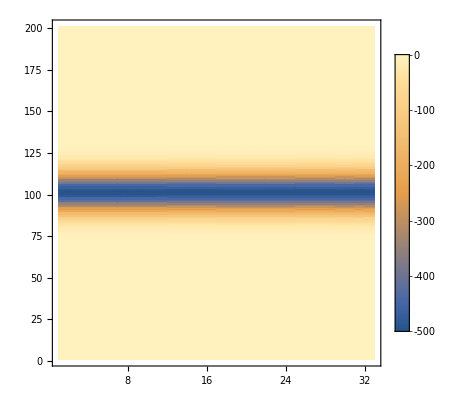

```mathematica
v2[x_,y_,A_,d_,w_]:=A Exp[-(y-d)^2 4Log[2]/w^2]
v2plot=Table[v2[x,y,Famp,Fpos,Fwth],{x,x2},{y,x3}];
ListLinePlot[Transpose[{x3,v2plot[[1,;;]]}],PlotRange->All,GridLines->{Fpos+Fwth{-1,1}/2,{Famp/2}}]
ListDensityPlot[v2plot//Transpose,InterpolationOrder->0,PlotLegends->Automatic,PlotRange->All]
```

## All Latitudinal Cuts

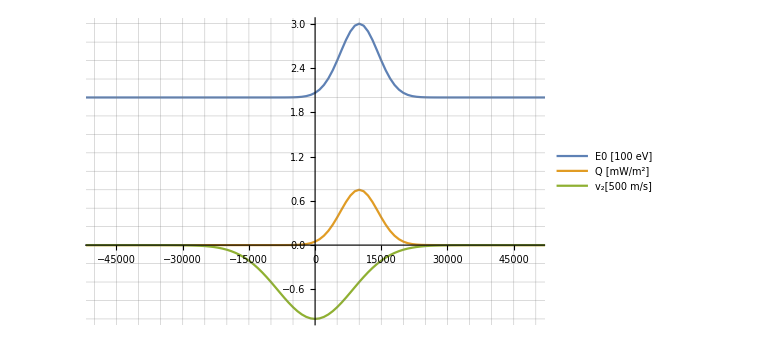

```mathematica
ListLinePlot[{
Transpose[{x3,E0plot[[1,;;]]/100}]
,Transpose[{x3,Qplot[[1,;;]]}]
,Transpose[{x3,v2plot[[1,;;]]/500}]
}
,PlotRange->{{-50000,50000},All}
,PlotLegends->{"E0 [100 eV]","Q [mW/m^2]","v_2[500 m/s]"}
,ImageSize->Large
,GridLines->All
]
```

## Electric Potential

```mathematica
E3[x_,y_,v2A_,d_,w_,B_]:=-v2[x,y,v2A,d,w]B
FullSimplify[-Integrate[E3[x,y,v2A,d,w,B],y]]
```

-1/4 B v2A w Erf[(2 (d-y) √Log[2])/w] √(π/Log[2])

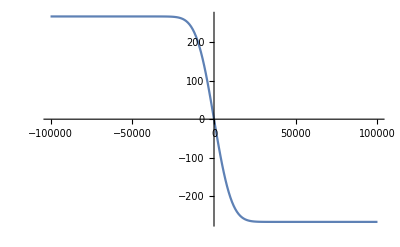

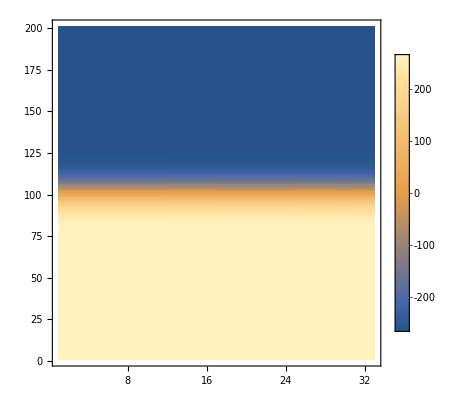

```mathematica
ϕ[x_,y_,v2A_,d_,w_,B_]:=-Sqrt[π/(16Log[2])]v2A B w Erf[2Sqrt[Log[2]](d-y)/w]
ϕplot=Table[ϕ[x,y,Famp,Fpos,Fwth,Bmag],{x,x2},{y,x3}];
ListLinePlot[Transpose[{x3,ϕplot[[1,;;]]}],PlotRange->All]
ListDensityPlot[ϕplot//Transpose,InterpolationOrder->0,PlotLegends->Automatic,PlotRange->All]
```

```mathematica
(-(-D[ϕ[x,y,v2A,d,w,B],y])/B)/v2[x,y,v2A,d,w]//FullSimplify
```

1

## Field-Aligned Current

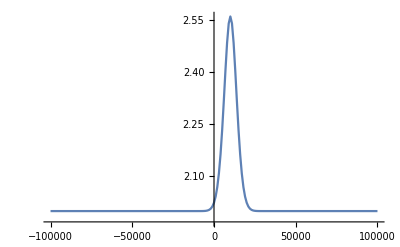

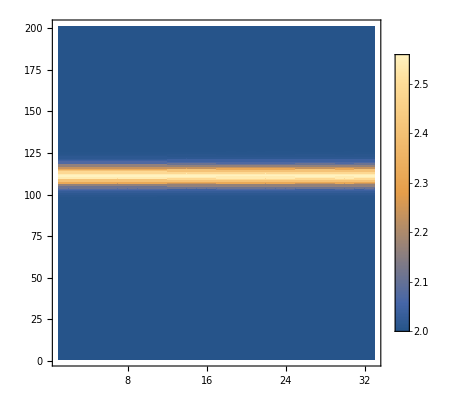

```mathematica
ΣP[x_,y_,QA_,E0A_,E0Ab_,d_,w_]:=2+Q[x,y,QA,d,w]Sqrt[((40(E0[x,y,E0A,E0Ab,d,w] 10^-3))/(16+(E0[x,y,E0A,E0Ab,d,w] 10^-3)^2))^2+0(5.7)^2]
ΣPplot=Table[ΣP[x,y,Qamp, Eamp, Emin,Epos,Ewth],{x,x2},{y,x3}];
ListLinePlot[Transpose[{x3,ΣPplot[[1,;;]]}],PlotRange->All]
ListDensityPlot[ΣPplot//Transpose,InterpolationOrder->0,PlotLegends->Automatic,PlotRange->All]
```

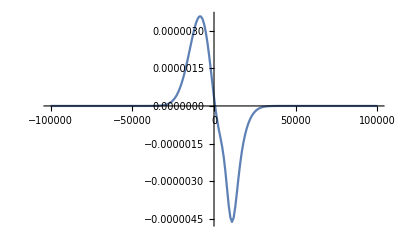

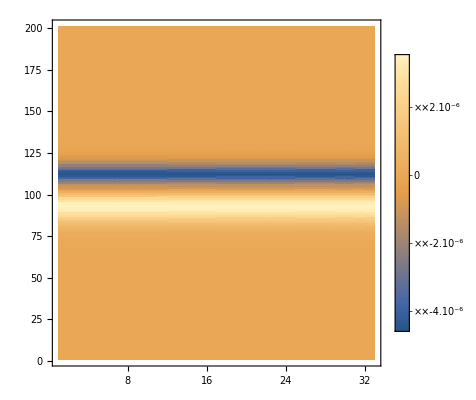

```mathematica
j[x_,y_,QA_,E0A_,E0Ab_,v2A_,pd_,pw_,vd_,vw_,B_]:=D[ΣP[x,yp,QA,E0A,E0Ab,pd,pw]E3[x,yp,v2A,vd,vw,B],yp]/.yp->y
jplot=Table[j[x,y,Qamp, Eamp, Emin,Famp,Epos,Ewth,Fpos,Fwth,Bmag],{x,x2},{y,x3}];
ListLinePlot[Transpose[{x3,jplot[[1,;;]]}],PlotRange->All]
ListDensityPlot[jplot//Transpose,InterpolationOrder->0,PlotLegends->Automatic,PlotRange->All]
```

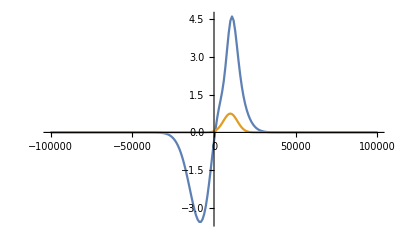

```mathematica
ListLinePlot[{
Transpose[{x3,-jplot[[1,;;]] 10^6}]
,Transpose[{x3,Qplot[[1,;;]]}]
}
,PlotRange->All]
```

## GEMINI Imports

```mathematica
run="grace_crex_03";
x3gemini=Import["\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\public_html\\Gemini3D\\"<>run<>"\\inputs\\simgrid.h5","/x3"][[3;;-3]];
E0p=Import["\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\public_html\\Gemini3D\\"<>run<>"\\inputs\\particles\\20211201_34050.000000.h5","/E0p"];
Qp=Import["\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\public_html\\Gemini3D\\"<>run<>"\\inputs\\particles\\20211201_34050.000000.h5","/Qp"];
Vmaxx1it=Import["\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\public_html\\Gemini3D\\"<>run<>"\\inputs\\fields\\20211201_34050.000000.h5","/Vmaxx1it"];
J1all=Import["\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\public_html\\Gemini3D\\"<>run<>"\\20211201_33760.000000.h5","/J1all"];
J1allLast=Import["\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\public_html\\Gemini3D\\"<>run<>"\\20211201_34050.000000.h5","/J1all"];
```

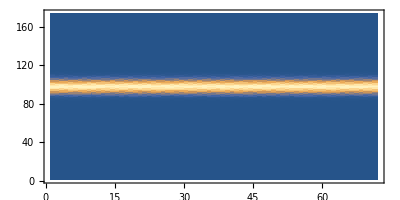

```mathematica
ListDensityPlot[E0p,InterpolationOrder->0,AspectRatio->1/2,PlotRange->All,PlotLegends->Automatic]
```

```mathematica
ListDensityPlot[Qp,InterpolationOrder->0,AspectRatio->1/2,PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

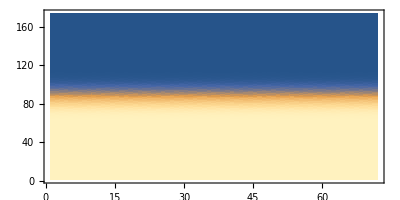

```mathematica
ListDensityPlot[Vmaxx1it,InterpolationOrder->0,AspectRatio->1/2,PlotLegends->Automatic]
```

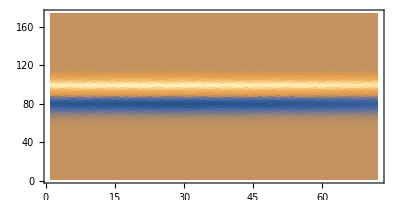

```mathematica
ListDensityPlot[J1all[[;;,;;,-1]],InterpolationOrder->0,AspectRatio->1/2,PlotLegends->Automatic,PlotRange->All]
```

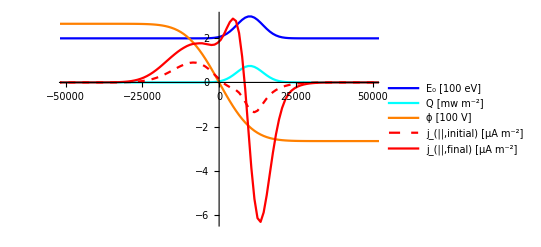

```mathematica
ListLinePlot[{
Transpose[{x3gemini,E0p[[;;,144/2]]/100}]
,Transpose[{x3gemini,Qp[[;;,144/2]]}]
,Transpose[{x3gemini,Vmaxx1it[[;;,144/2]]/ 100}]
,Transpose[{x3gemini,-J1all[[;;,144/2,-1]] 10^6}]
,Transpose[{x3gemini,-J1allLast[[;;,144/2,-1]] 10^6}]
}
,PlotRange->{{-50000,50000},All}
,PlotStyle->{Blue,Cyan,Orange,{Red,Dashed},Red}
,PlotLegends->{"E_0 [100 eV]","Q [mw m^-2]","ϕ [100 V]","j_(||,initial) [μA m^-2]","j_(||,final) [μA m^-2]"}
]
```

# LAMP GEMINI Inputs

```mathematica
x2=Range[- 10^5,10^5,1.6282 10^3];
x3=Range[- 10^5,10^5,1.6282 10^3];
Bmag=50000 10^-9;
```

## Precipitation

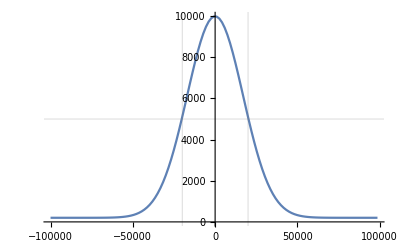

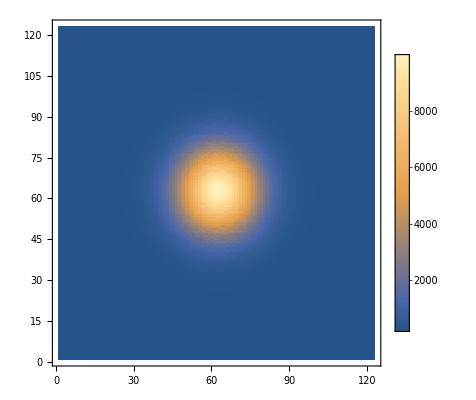

```mathematica
E0[x_,y_,A_,Ab_,w_]:=(A-Ab) Exp[-(x^2+y^2)4Log[2]/w^2]+Ab
E0plot=Table[E0[x,y,10000,200,40000],{x,x2},{y,x3}];
ListLinePlot[Transpose[{x3,E0plot[[Round[Length[x2]/2],;;]]}],PlotRange->All,GridLines->{20000{-1,1},{5000}}]
ListDensityPlot[E0plot//Transpose,InterpolationOrder->0,PlotLegends->Automatic,PlotRange->All]
```

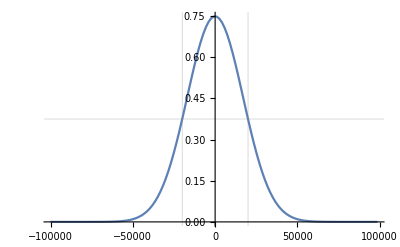

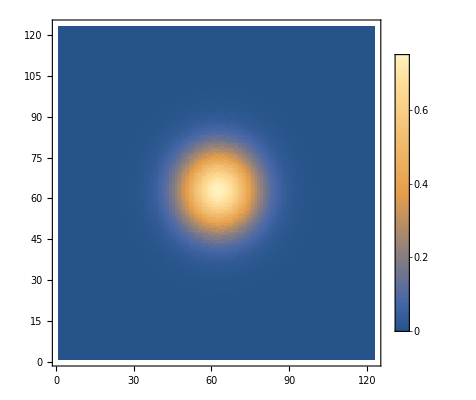

```mathematica
Q[x_,y_,A_,w_]:=A Exp[-(x^2+y^2)4Log[2]/w^2]
Qplot=Table[Q[x,y,0.75,40000],{x,x2},{y,x3}];
ListLinePlot[Transpose[{x3,Qplot[[Round[Length[x2]/2],;;]]}],PlotRange->All,GridLines->{20000{-1,1},{0.75/2}}]
ListDensityPlot[Qplot//Transpose,InterpolationOrder->0,PlotLegends->Automatic,PlotRange->All]
```

## Flow Burst